# Nuclear Astrophysics : -

## Penetration Factor Calculation for proton capture by ^9 Be :-

### Parameters : -

```mathematica
z1 = 4;
z2=1;
A1=9;
A2=1;
μ= ((A1*931.5)*(A2*931.5))/((A1*931.5)+(A2*931.5));
l=3/2;
l0=3/2;
a0=1.2;  (*FemtoMeter*)
r= a0*A1^(1/3);
α= 1/137;(*Dimensionless*)
e0=1.29;
k=Sqrt[2μ*ei]/197.3; (*197.3 MeV fm*)
ρ=k*r;
η =((z1)*(z2)*α *(Sqrt[μ/(2ei)]));
k0=Sqrt[2μ*e0]/197.3;
ρ0=k0*r;
η0 =((z1)*(z2)*α *(Sqrt[μ/(2e0)]));
FC[ρ_,l_,η_]:=Re[(E^(-π η/2-ⅈ ρ) Abs[Gamma[1+l+ ⅈ η]])/(2 Gamma[2(l+1)]) (2 ρ)^(l+1)Hypergeometric1F1[1+l-ⅈ η,2 (1+l),2 ⅈ ρ]];
GC[ρ_,l_,η_]:=Im[ (E^(π η/2-ⅈ ρ) Gamma[1+l- ⅈ η])/Abs[Gamma[1+l+ ⅈ η]]   (-2ρ)^(l+1) HypergeometricU[1+l-ⅈ η,2 (1+l),2 ⅈ ρ]];
FC[ρ0_,l0_,η0_]:=Re[(E^(-π η0/2-ⅈ ρ0) Abs[Gamma[1+l0+ ⅈ η0]])/(2 Gamma[2(l0+1)]) (2 ρ0)^(l0+1)Hypergeometric1F1[1+l0-ⅈ η0,2 (1+l0),2 ⅈ ρ0]];
GC[ρ0_,l0_,η0_]:=Im[ (E^(π η0/2-ⅈ ρ0) Gamma[1+l0- ⅈ η0])/Abs[Gamma[1+l0+ ⅈ η0]]   (-2ρ0)^(l0+1) HypergeometricU[1+l0-ⅈ η0,2 (1+l0),2 ⅈ ρ0]];
```

```mathematica
p0=ρ0/((FC[ρ0,l0,η0])^2+(GC[ρ0,l0,η0])^2);
```

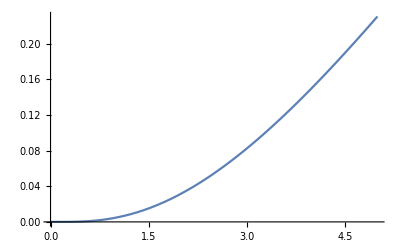

```mathematica
p=ρ/((FC[ρ,l,η])^2+(GC[ρ,l,η])^2);
Plot[p,{ei,0,5}]
```

### PLOT : -

```mathematica
p0= ρ/((FC[ρ,0,η])^2+(GC[ρ,0,η])^2);
p1= ρ/((FC[ρ,1,η])^2+(GC[ρ,1,η])^2);
p2= ρ/((FC[ρ,2,η])^2+(GC[ρ,2,η])^2);
p3= ρ/((FC[ρ,3,η])^2+(GC[ρ,3,η])^2);
```

```mathematica
Plot[{p0,p1,p2,p3},{ei,0,5},PlotLabels->{"l=0","l=1","l=2","l=3"}]
```

-Graphics-

## PROTON GAMMA WIDTH (1.7 MeV) : -

0.233

(0.233 (1.07346 Im[(ⅇ^(0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) √ei Gamma[1-(0.+0.597774 ⅈ) √(1/ei)] HypergeometricU[1-(0.+0.597774 ⅈ) √(1/ei),2,(0.+1.03608 ⅈ) √ei])/Abs[Gamma[1+(0.+0.597774 ⅈ) √(1/ei)]]]^2+0.268365 Re[ⅇ^(-0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) √ei Abs[Gamma[1+(0.+0.597774 ⅈ) √(1/ei)]] Hypergeometric1F1[1-(0.+0.597774 ⅈ) √(1/ei),2,(0.+1.03608 ⅈ) √ei]]^2))/(1.19389 Im[(ⅇ^(0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) (-√ei)^(5/2) Gamma[5/2-(0.+0.597774 ⅈ) √(1/ei)] HypergeometricU[5/2-(0.+0.597774 ⅈ) √(1/ei),5,(0.+1.03608 ⅈ) √ei])/Abs[Gamma[5/2+(0.+0.597774 ⅈ) √(1/ei)]]]^2+0.00051818 Re[ⅇ^(-0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) ei^(5/4) Abs[Gamma[5/2+(0.+0.597774 ⅈ) √(1/ei)]] Hypergeometric1F1[5/2-(0.+0.597774 ⅈ) √(1/ei),5,(0.+1.03608 ⅈ) √ei]]^2)

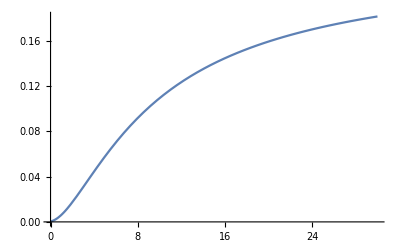

```mathematica
Γger = 0.27*10^-6;
Γ=233*10^-3;
Γper = Γ-Γger
Γpe = p/p0* Γper 
Plot[Γpe ,{ei,0,30}]
```

## GAMMA GAMMA WIDTH (1.7 MeV) : -

```mathematica
ef=6.58;
ji1 = 3/2+1/2;
ji2 = 3/2-1/2;
jf= 1/2;

λ = 2; (*Change*)
Γge = ((ei+ ef)/(e0+ef))^(2λ+1)* Γger
```

8.94314×10^-12 (6.58+ei)^5

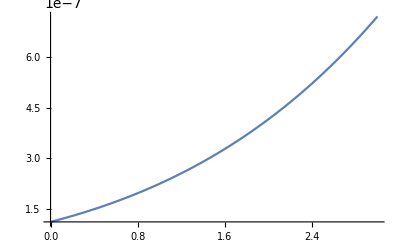

```mathematica
Plot[Γge ,{ei,0,3}]
```

## Cross section of proton capture by Carbon-12: -

```mathematica
J =2;(*Change*)
I1 = 1/2;
I2 = 1/2;


ω = (1+ 1 )((2*J) +1)/(((2*I1) +1)((2*I2 )+1));

Γt=Γpe+Γge;

σe = 3.14/k^2*ω*(Γpe*Γge)/((ei-e0)^2+(Γt)^2/4)
```

(3.79764×10^-10 (6.58+ei)^5 (1.07346 Im[(ⅇ^(0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) √ei Gamma[1-(0.+0.597774 ⅈ) √(1/ei)] HypergeometricU[1-(0.+0.597774 ⅈ) √(1/ei),2,(0.+1.03608 ⅈ) √ei])/Abs[Gamma[1+(0.+0.597774 ⅈ) √(1/ei)]]]^2+0.268365 Re[ⅇ^(-0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) √ei Abs[Gamma[1+(0.+0.597774 ⅈ) √(1/ei)]] Hypergeometric1F1[1-(0.+0.597774 ⅈ) √(1/ei),2,(0.+1.03608 ⅈ) √ei]]^2))/(ei (1.19389 Im[(ⅇ^(0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) (-√ei)^(5/2) Gamma[5/2-(0.+0.597774 ⅈ) √(1/ei)] HypergeometricU[5/2-(0.+0.597774 ⅈ) √(1/ei),5,(0.+1.03608 ⅈ) √ei])/Abs[Gamma[5/2+(0.+0.597774 ⅈ) √(1/ei)]]]^2+0.00051818 Re[ⅇ^(-0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) ei^(5/4) Abs[Gamma[5/2+(0.+0.597774 ⅈ) √(1/ei)]] Hypergeometric1F1[5/2-(0.+0.597774 ⅈ) √(1/ei),5,(0.+1.03608 ⅈ) √ei]]^2) ((-1.29+ei)^2+1/4 (8.94314×10^-12 (6.58+ei)^5+(0.233 (1.07346 Im[(ⅇ^(0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) √ei Gamma[1-(0.+0.597774 ⅈ) √(1/ei)] HypergeometricU[1-(0.+0.597774 ⅈ) √(1/ei),2,(0.+1.03608 ⅈ) √ei])/Abs[Gamma[1+(0.+0.597774 ⅈ) √(1/ei)]]]^2+0.268365 Re[ⅇ^(-0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) √ei Abs[Gamma[1+(0.+0.597774 ⅈ) √(1/ei)]] Hypergeometric1F1[1-(0.+0.597774 ⅈ) √(1/ei),2,(0.+1.03608 ⅈ) √ei]]^2))/(1.19389 Im[(ⅇ^(0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) (-√ei)^(5/2) Gamma[5/2-(0.+0.597774 ⅈ) √(1/ei)] HypergeometricU[5/2-(0.+0.597774 ⅈ) √(1/ei),5,(0.+1.03608 ⅈ) √ei])/Abs[Gamma[5/2+(0.+0.597774 ⅈ) √(1/ei)]]]^2+0.00051818 Re[ⅇ^(-0.938981 √(1/ei)-(0.+0.518039 ⅈ) √ei) ei^(5/4) Abs[Gamma[5/2+(0.+0.597774 ⅈ) √(1/ei)]] Hypergeometric1F1[5/2-(0.+0.597774 ⅈ) √(1/ei),5,(0.+1.03608 ⅈ) √ei]]^2))^2))

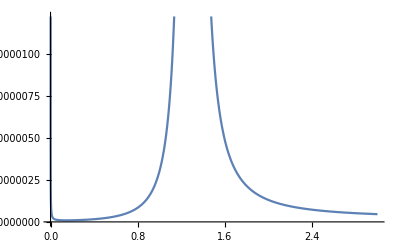

```mathematica
Plot[σe,{ei,0,3}]
```

## Astrophysical S-Factor:

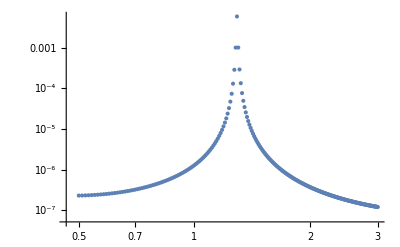

```mathematica
points=Table[{ei,Se=ei/ⅇ^(-2*Pi*η)*σe*10^-2},{ei,Range[0.5,3,0.01]}];

ListLogLogPlot[points]
```

```mathematica
Shallow[points]
Export["points.txt",points,"Table"]
```

{{0.5,2.30898×10^-7},{0.51,2.31924×10^-7},{0.52,2.33314×10^-7},{0.53,2.3506×10^-7},{0.54,2.37157×10^-7},{0.55,2.39603×10^-7},{0.56,2.42398×10^-7},{0.57,2.45544×10^-7},{0.58,2.49045×10^-7},{0.59,2.52906×10^-7},«241»}

points.txt

```mathematica
Export["filename.xls",Table[{ei,Se},{ei,0,2,0.05}]];
SeTable=Table[0,{n,1,200}];
```

```mathematica
ei=0; dei=0.01;
```

```mathematica
Do[ei=ei+dei;
STable[[n]]={ei,S};
Print[ei, "  ", Se],
{n,1,200}]
```

Set::noval: Symbol STable in part assignment does not have an immediate value.

0.01  1.20936×10^-7

Set::noval: Symbol STable in part assignment does not have an immediate value.

0.02  1.20936×10^-7

Set::noval: Symbol STable in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

0.03  1.20936×10^-7

0.04  1.20936×10^-7

0.05  1.20936×10^-7

0.06  1.20936×10^-7

0.07  1.20936×10^-7

0.08  1.20936×10^-7

0.09  1.20936×10^-7

0.1  1.20936×10^-7

0.11  1.20936×10^-7

0.12  1.20936×10^-7

0.13  1.20936×10^-7

0.14  1.20936×10^-7

0.15  1.20936×10^-7

0.16  1.20936×10^-7

0.17  1.20936×10^-7

0.18  1.20936×10^-7

0.19  1.20936×10^-7

0.2  1.20936×10^-7

0.21  1.20936×10^-7

0.22  1.20936×10^-7

0.23  1.20936×10^-7

0.24  1.20936×10^-7

0.25  1.20936×10^-7

0.26  1.20936×10^-7

0.27  1.20936×10^-7

0.28  1.20936×10^-7

0.29  1.20936×10^-7

0.3  1.20936×10^-7

0.31  1.20936×10^-7

0.32  1.20936×10^-7

0.33  1.20936×10^-7

0.34  1.20936×10^-7

0.35  1.20936×10^-7

0.36  1.20936×10^-7

0.37  1.20936×10^-7

0.38  1.20936×10^-7

0.39  1.20936×10^-7

0.4  1.20936×10^-7

0.41  1.20936×10^-7

0.42  1.20936×10^-7

0.43  1.20936×10^-7

0.44  1.20936×10^-7

0.45  1.20936×10^-7

0.46  1.20936×10^-7

0.47  1.20936×10^-7

0.48  1.20936×10^-7

0.49  1.20936×10^-7

0.5  1.20936×10^-7

0.51  1.20936×10^-7

0.52  1.20936×10^-7

0.53  1.20936×10^-7

0.54  1.20936×10^-7

0.55  1.20936×10^-7

0.56  1.20936×10^-7

0.57  1.20936×10^-7

0.58  1.20936×10^-7

0.59  1.20936×10^-7

0.6  1.20936×10^-7

0.61  1.20936×10^-7

0.62  1.20936×10^-7

0.63  1.20936×10^-7

0.64  1.20936×10^-7

0.65  1.20936×10^-7

0.66  1.20936×10^-7

0.67  1.20936×10^-7

0.68  1.20936×10^-7

0.69  1.20936×10^-7

0.7  1.20936×10^-7

0.71  1.20936×10^-7

0.72  1.20936×10^-7

0.73  1.20936×10^-7

0.74  1.20936×10^-7

0.75  1.20936×10^-7

0.76  1.20936×10^-7

0.77  1.20936×10^-7

0.78  1.20936×10^-7

0.79  1.20936×10^-7

0.8  1.20936×10^-7

0.81  1.20936×10^-7

0.82  1.20936×10^-7

0.83  1.20936×10^-7

0.84  1.20936×10^-7

0.85  1.20936×10^-7

0.86  1.20936×10^-7

0.87  1.20936×10^-7

0.88  1.20936×10^-7

0.89  1.20936×10^-7

0.9  1.20936×10^-7

0.91  1.20936×10^-7

0.92  1.20936×10^-7

0.93  1.20936×10^-7

0.94  1.20936×10^-7

0.95  1.20936×10^-7

0.96  1.20936×10^-7

0.97  1.20936×10^-7

0.98  1.20936×10^-7

0.99  1.20936×10^-7

1.  1.20936×10^-7

1.01  1.20936×10^-7

1.02  1.20936×10^-7

1.03  1.20936×10^-7

1.04  1.20936×10^-7

1.05  1.20936×10^-7

1.06  1.20936×10^-7

1.07  1.20936×10^-7

1.08  1.20936×10^-7

1.09  1.20936×10^-7

1.1  1.20936×10^-7

1.11  1.20936×10^-7

1.12  1.20936×10^-7

1.13  1.20936×10^-7

1.14  1.20936×10^-7

1.15  1.20936×10^-7

1.16  1.20936×10^-7

1.17  1.20936×10^-7

1.18  1.20936×10^-7

1.19  1.20936×10^-7

1.2  1.20936×10^-7

1.21  1.20936×10^-7

1.22  1.20936×10^-7

1.23  1.20936×10^-7

1.24  1.20936×10^-7

1.25  1.20936×10^-7

1.26  1.20936×10^-7

1.27  1.20936×10^-7

1.28  1.20936×10^-7

1.29  1.20936×10^-7

1.3  1.20936×10^-7

1.31  1.20936×10^-7

1.32  1.20936×10^-7

1.33  1.20936×10^-7

1.34  1.20936×10^-7

1.35  1.20936×10^-7

1.36  1.20936×10^-7

1.37  1.20936×10^-7

1.38  1.20936×10^-7

1.39  1.20936×10^-7

1.4  1.20936×10^-7

1.41  1.20936×10^-7

1.42  1.20936×10^-7

1.43  1.20936×10^-7

1.44  1.20936×10^-7

1.45  1.20936×10^-7

1.46  1.20936×10^-7

1.47  1.20936×10^-7

1.48  1.20936×10^-7

1.49  1.20936×10^-7

1.5  1.20936×10^-7

1.51  1.20936×10^-7

1.52  1.20936×10^-7

1.53  1.20936×10^-7

1.54  1.20936×10^-7

1.55  1.20936×10^-7

1.56  1.20936×10^-7

1.57  1.20936×10^-7

1.58  1.20936×10^-7

1.59  1.20936×10^-7

1.6  1.20936×10^-7

1.61  1.20936×10^-7

1.62  1.20936×10^-7

1.63  1.20936×10^-7

1.64  1.20936×10^-7

1.65  1.20936×10^-7

1.66  1.20936×10^-7

1.67  1.20936×10^-7

1.68  1.20936×10^-7

1.69  1.20936×10^-7

1.7  1.20936×10^-7

1.71  1.20936×10^-7

1.72  1.20936×10^-7

1.73  1.20936×10^-7

1.74  1.20936×10^-7

1.75  1.20936×10^-7

1.76  1.20936×10^-7

1.77  1.20936×10^-7

1.78  1.20936×10^-7

1.79  1.20936×10^-7

1.8  1.20936×10^-7

1.81  1.20936×10^-7

1.82  1.20936×10^-7

1.83  1.20936×10^-7

1.84  1.20936×10^-7

1.85  1.20936×10^-7

1.86  1.20936×10^-7

1.87  1.20936×10^-7

1.88  1.20936×10^-7

1.89  1.20936×10^-7

1.9  1.20936×10^-7

1.91  1.20936×10^-7

1.92  1.20936×10^-7

1.93  1.20936×10^-7

1.94  1.20936×10^-7

1.95  1.20936×10^-7

1.96  1.20936×10^-7

1.97  1.20936×10^-7

1.98  1.20936×10^-7

1.99  1.20936×10^-7

2.  1.20936×10^-7